## Get helper functions

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"UTILITY_readBeamFiles.nb"}]]
```

## Import

Copy-paste output of “2025-02-07 Parallelized L1, L2 phase scan.py”

```mathematica
importInfo="-30, -40, -30_-40.h5
-25, -40, -25_-40.h5
-20, -40, -20_-40.h5
-15, -40, -15_-40.h5
-10, -40, -10_-40.h5
-5, -40, -5_-40.h5
-30, -38, -30_-38.h5
-25, -38, -25_-38.h5
-20, -38, -20_-38.h5
-15, -38, -15_-38.h5
-10, -38, -10_-38.h5
-5, -38, -5_-38.h5
-30, -36, -30_-36.h5
-25, -36, -25_-36.h5
-20, -36, -20_-36.h5
-15, -36, -15_-36.h5
-10, -36, -10_-36.h5
-5, -36, -5_-36.h5
-30, -34, -30_-34.h5
-25, -34, -25_-34.h5
-20, -34, -20_-34.h5
-15, -34, -15_-34.h5
-10, -34, -10_-34.h5
-5, -34, -5_-34.h5
-30, -32, -30_-32.h5
-25, -32, -25_-32.h5
-20, -32, -20_-32.h5
-15, -32, -15_-32.h5
-10, -32, -10_-32.h5
-5, -32, -5_-32.h5
-30, -30, -30_-30.h5
-25, -30, -25_-30.h5
-20, -30, -20_-30.h5
-15, -30, -15_-30.h5
-10, -30, -10_-30.h5
-5, -30, -5_-30.h5";
importInfo = ImportString[importInfo]
```

{{-30,-40,-30_-40.h5},{-25,-40,-25_-40.h5},{-20,-40,-20_-40.h5},{-15,-40,-15_-40.h5},{-10,-40,-10_-40.h5},{-5,-40,-5_-40.h5},{-30,-38,-30_-38.h5},{-25,-38,-25_-38.h5},{-20,-38,-20_-38.h5},{-15,-38,-15_-38.h5},{-10,-38,-10_-38.h5},{-5,-38,-5_-38.h5},{-30,-36,-30_-36.h5},{-25,-36,-25_-36.h5},{-20,-36,-20_-36.h5},{-15,-36,-15_-36.h5},{-10,-36,-10_-36.h5},{-5,-36,-5_-36.h5},{-30,-34,-30_-34.h5},{-25,-34,-25_-34.h5},{-20,-34,-20_-34.h5},{-15,-34,-15_-34.h5},{-10,-34,-10_-34.h5},{-5,-34,-5_-34.h5},{-30,-32,-30_-32.h5},{-25,-32,-25_-32.h5},{-20,-32,-20_-32.h5},{-15,-32,-15_-32.h5},{-10,-32,-10_-32.h5},{-5,-32,-5_-32.h5},{-30,-30,-30_-30.h5},{-25,-30,-25_-30.h5},{-20,-30,-20_-30.h5},{-15,-30,-15_-30.h5},{-10,-30,-10_-30.h5},{-5,-30,-5_-30.h5}}

```mathematica
L1Values = importInfo[[All,1]]//DeleteDuplicates
L2Values=importInfo[[All,2]]//DeleteDuplicates

importInfo=Association[(({#[[1]],#[[2]]}->NotebookDirectory[]<>#[[3]])&/@importInfo)]
```

{-30,-25,-20,-15,-10,-5}

{-40,-38,-36,-34,-32,-30}

<|{-30,-40}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-30_-40.h5,{-25,-40}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-25_-40.h5,{-20,-40}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-20_-40.h5,{-15,-40}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-15_-40.h5,{-10,-40}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-10_-40.h5,{-5,-40}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-5_-40.h5,{-30,-38}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-30_-38.h5,{-25,-38}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-25_-38.h5,{-20,-38}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-20_-38.h5,{-15,-38}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-15_-38.h5,{-10,-38}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-10_-38.h5,{-5,-38}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-5_-38.h5,{-30,-36}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-30_-36.h5,{-25,-36}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-25_-36.h5,{-20,-36}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-20_-36.h5,{-15,-36}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-15_-36.h5,{-10,-36}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-10_-36.h5,{-5,-36}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-5_-36.h5,{-30,-34}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-30_-34.h5,{-25,-34}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-25_-34.h5,{-20,-34}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-20_-34.h5,{-15,-34}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-15_-34.h5,{-10,-34}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-10_-34.h5,{-5,-34}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-5_-34.h5,{-30,-32}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-30_-32.h5,{-25,-32}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-25_-32.h5,{-20,-32}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-20_-32.h5,{-15,-32}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-15_-32.h5,{-10,-32}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-10_-32.h5,{-5,-32}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-5_-32.h5,{-30,-30}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-30_-30.h5,{-25,-30}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-25_-30.h5,{-20,-30}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-20_-30.h5,{-15,-30}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-15_-30.h5,{-10,-30}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-10_-30.h5,{-5,-30}→/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-5_-30.h5|>

## Test approach

```mathematica
fileName = (Values[importInfo][[1]])
data = readBeamFile[fileName];
```

/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/-30_-40.h5

```mathematica
lpsData = {#z,#pz}&/@data;
meanZ = Mean[lpsData[[All,1]]];


lpsData = {10^6 (#[[1]]-meanZ),10^-9(#[[2]])}&/@lpsData;

energyRange = {9.8,10.2};
zRange ={-100,100};
lpsData = Select[
lpsData,
zRange[[1]]<#[[1]]<zRange[[2]]&&energyRange[[1]]<#[[2]]<energyRange[[2]]&
];



lpsImg = densityHistogramMod[
lpsData,
{400,400},
LabelStyle->20,
ImageSize->800,
PlotRange->{zRange,energyRange},
FrameLabel->{"ζ [mm]","E [GeV]"},
PlotRangePadding->None
];




currentBinSizeμm = 1.0;
binLoc =MovingAverage[Range[zRange[[1]],zRange[[2]],currentBinSizeμm],2];
binCounts = BinCounts[lpsData[[All,1]],{zRange[[1]],zRange[[2]],currentBinSizeμm}];




smoothingRadius =3;
binnedCurrentData = Transpose[{
GaussianFilter[binLoc,smoothingRadius],
GaussianFilter[binCounts,smoothingRadius]
}];


maxCounts = 8000;
binnedCurrentData[[All,2]]=Rescale[#,{0,maxCounts},energyRange]&/@binnedCurrentData[[All,2]];


currentImg = ListPlot[binnedCurrentData,PlotRange->{zRange,energyRange},Axes->False,PlotStyle->White,Joined->True,ImageSize->800];

Rasterize[
Show[lpsImg,currentImg],
RasterSize->800
]
```

-Graphics-

## Process

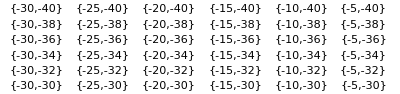

```mathematica
imgArr =Table[
{L1,L2},
{L2,L2Values},
{L1,L1Values}
];
GraphicsGrid[imgArr]
```

```mathematica
imgArr =ParallelTable[
fileName = (importInfo[{L1,L2}]);
data = readBeamFile[fileName];


lpsData = {#z,#pz}&/@data;
meanZ = Mean[lpsData[[All,1]]];


lpsData = {10^6 (#[[1]]-meanZ),10^-9(#[[2]])}&/@lpsData;

energyRange = {9.8,10.2};
zRange ={-100,100};
lpsData = Select[
lpsData,
zRange[[1]]<#[[1]]<zRange[[2]]&&energyRange[[1]]<#[[2]]<energyRange[[2]]&
];



lpsImg = densityHistogramMod[
lpsData,
{400,400},
LabelStyle->20,
ImageSize->800,
PlotRange->{zRange,energyRange},
FrameLabel->{"ζ [mm]","E [GeV]"},
PlotRangePadding->None
];




currentBinSizeμm = 1.0;
binLoc =MovingAverage[Range[zRange[[1]],zRange[[2]],currentBinSizeμm],2];
binCounts = BinCounts[lpsData[[All,1]],{zRange[[1]],zRange[[2]],currentBinSizeμm}];




smoothingRadius =3;
binnedCurrentData = Transpose[{
GaussianFilter[binLoc,smoothingRadius],
GaussianFilter[binCounts,smoothingRadius]
}];


maxCounts = 8000;
binnedCurrentData[[All,2]]=Rescale[#,{0,maxCounts},energyRange]&/@binnedCurrentData[[All,2]];


currentImg = ListPlot[binnedCurrentData,PlotRange->{zRange,energyRange},Axes->False,PlotStyle->White,Joined->True,ImageSize->800];

Rasterize[
Show[lpsImg,currentImg],
RasterSize->800
],
{L2,L2Values},
{L1,L1Values}
];
```

```mathematica
GraphicsGrid[imgArr,ImageSize->3000]
```

-Graphics-